2 √2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2)-1/2 ⅈ p^2 t)

(2 √2 ⅇ^(-64+(ⅈ ((12-32 ⅈ)+x)^2)/(2 (-8 ⅈ+t))))/(√(8+ⅈ t))

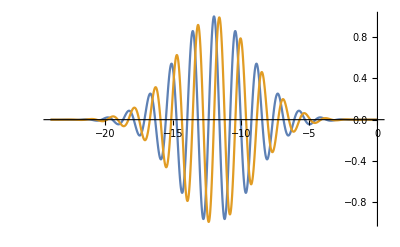

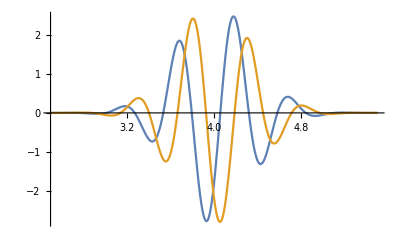

```mathematica
ћ=1;
m=1;
a=4;
x0=-12;
p0=4;
ψ=Exp[-((x-x0)/a)^2+ⅈ p0(x-x0)/ћ];
ϕ=InverseFourierTransform[ψ,x,p];
ϕt=ϕ Exp[-ⅈ p^2 t/(2m ћ)]
ψt=FourierTransform[ϕt,p,x]
Plot[{Re[ψ],Im[ψ]},{x,-3a+x0,3a +x0},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ],Im[ϕ]},{p,-6/a+p0,6/a +p0},PlotRange->All,PlotPoints->150]
```